# Special Conformal Transformations

A special conformal transformation in 2D is a composition of an inversion, a translation, and an inversion. An inversion maps x^i→ x^i/x^2, and a translation maps x^i→x^i+ a^i.

```mathematica
(*Define special conformal transformation, parametrized by translation vector (a1,a2)*)
y1[x1_,x2_,a1_,a2_]:=(x1+(x1^2+x2^2)a1)/(1+2(x1 a1+x2 a2)+(x1^2+x2^2)(a1^2+a2^2))
y2[x1_,x2_,a1_,a2_]:=(x2+(x1^2+x2^2)a2)/(1+2(x1 a1+x2 a2)+(x1^2+x2^2)(a1^2+a2^2))
```

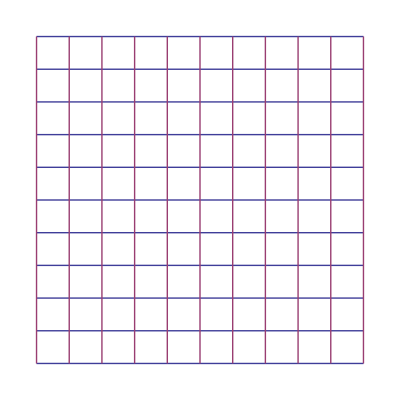

```mathematica
(*Original grid*)
ParametricPlot[
{Table[{t,n},{n,-5,5}],Table[{n,t},{n,-5,5}]},{t,-5,5},
Axes->False]
```

```mathematica
(*Grid after special conformal transformation, parametrized by translation vector (a1,a2)*)
Manipulate[ParametricPlot[{Table[{y1[t,n,a1,a2],y2[t,n,a1,a2]},{n,-5,5}],Table[{y1[n,t,a1,a2],y2[n,t,a1,a2]},{n,-5,5}]},{t,-5,5},
PlotRange->{{-5,5},{-5,5}},
Axes->False
],
{{a1,0},-1,1},
{{a2,0},-1,1}]
```